```mathematica
g=9.8; (*grav. constant*)
θ=50*π/180;
v=30;
vt=35;
ode1={x''[t]==-g*x'[t]/vt^2*√(x'[t]^2+y'[t]^2),y''[t]==-g*(1+(y'[t]/vt^2*√(x'[t]^2+y'[t]^2))),x[0]==0,x'[0]==v*Cos[θ],y[0]==2,y'[0]==v*Sin[θ]};
sol=NDSolve[ode1,{x,y},{t,0,200}]
```

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

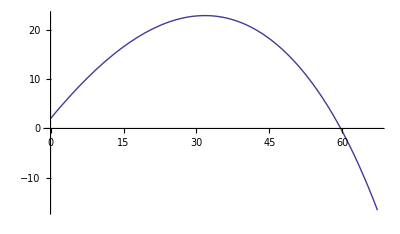

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,5},PlotRange-> All]
```

```mathematica
Manipulate[
g=9.8;
Module[
{result = NDSolve[{x''[t]==-g*x'[t]/vt^2*√(x'[t]^2+y'[t]^2),y''[t]==-g*(1+(y'[t]/vt^2*√(x'[t]^2+y'[t]^2))),x[0]==0,x'[0]==v*Cos[θ],y[0]==1.5,y'[0]==v*Sin[θ]},{x,y},{t,0,200}]},
ParametricPlot[{Evaluate[{x[t],y[t]}]/.result,{Evaluate[v*Cos[θ]*t,2+v*Sin[θ]*t-.5*g*t^2]}},{t,0,t2},PlotStyle-> {Red,Blue},AxesLabel->{"x (m)","y (m)"},PlotRange->All,ImageSize->{500,300}]],
{{v,30,"initial velocity (m/s)"},1,60,Appearance->"Labeled"},{{θ,50*Pi/180,"angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{vt,35,"terminal velocity (m/s)"},1,135.,Appearance->"Labeled"},{{t2,6,"time (s)"},1,20,Appearance->"Labeled"}]
```